```mathematica
NULLARRAY={999999,999999};
(*Parameters*)
LSIZE=2.0;
U0=0.0(*23.0*);
(*kappa=7.287781;*)
kappa=1.0;
SPTRUNC=5;(*N*)
DIM=2*SPTRUNC+1;
STATENO=1/2*DIM*(DIM+1);
Kdel[m_,n_]:=If[m==n,1,0];
psqmat[n_]:=(n-SPTRUNC-1)^2;


cmat[m_,n_]:= Module[{nloc,mloc},
nloc=n-SPTRUNC-1;
mloc=m-SPTRUNC-1;
If[(nloc==1 && mloc==0)||(nloc==0 && mloc==1),1/(√2),
If[(nloc>0&& mloc>0)||(nloc<0 && mloc<0),1/2*(Kdel[mloc,nloc+1]+Kdel[mloc,nloc-1]),
0.0]
]
];

GetPair[a1_,a2_,a3_,a4_]:=Module[{list},
If[a1==a2 && a3==a4,
list={a1,a3},
If[a1==a3 && a2==a4,
list={a1,a2},
If[a1==a4 && a2==a3,
list={a1,a3},
list=NULLARRAY;
];
];
];
list
];

inmat[m1_,n1_,m2_,n2_]:=Module[
{pair1,pair2,m1loc,m2loc,n1loc,n2loc,value},
m1loc=m1-SPTRUNC-1;
m2loc=m2-SPTRUNC-1;
n1loc=n1-SPTRUNC-1;
n2loc=n2-SPTRUNC-1;
value=0.0;
pairs=GetPair[m1loc,m2loc,n1loc,n2loc];
If[pairs==NULLARRAY,value=0.0,
pair1=pairs[[1]];
pair2=pairs[[2]];
If[pair1==pair2 && pair1 ≠0,value=0.75,Continue];
If[pair1==pair2 && pair2==0,value=0.50,Continue];

If[(pair1>0 && pair2==0)||(pair2>0 && pair1==0),value=0.50,Continue];
If[(pair1<0 && pair2==0)||(pair2<0 && pair1==0),value=0.50,Continue];
If[(pair1>0 && pair2<0)||(pair2>0 && pair1<0),value=0.50,Continue];

 If[pair1>0&& pair2>0 && pair1≠pair2,value=0.50,Continue];
If[pair1<0 && pair2<0 && pair1≠pair2,value=0.50,Continue];
 ];
value=2.0*U0*value/(LSIZE*Pi);
value

];

(*Single Particle hamiltonian*)
Honeptcl[n_,m_]:=psqmat[n]*Kdel[n,m] + kappa*cmat[n,m];


(*Build tower of states*)
(*Tower of 2-particle states*)
statetower=Table[0,{nt,1,STATENO}];
count=0;
For[i=1,i≤ DIM,i++,
      For[j=1,j≤i,j++,
             statetower[[count+1]]={i,j};
             count=count+1;
           ]
   ];


(*Build the hamiltonian matrix elements*)
Hamilt[n_,m_]:=Module[{n1,n2,m1,m2},n1=statetower[[n,1]];n2=statetower[[n,2]];m1=statetower[[m,1]];m2=statetower[[m,2]];Honeptcl[n1,m1]*Kdel[n2,m2]+Honeptcl[n1,m2]*Kdel[n2,m1]+Honeptcl[n2,m1]*Kdel[n1,m2]+Honeptcl[n2,m2]*Kdel[n1,m1]+inmat[m1,n1,m2,n2]];

Htwoptcl=Table[Hamilt[n,m],{n,1,STATENO},{m,1,STATENO}];
HEsys=Eigensystem[Htwoptcl];
SortedEnergies=HEsys[[1]];
SortedCoeff=HEsys[[2]];

(*Sort eigenvecotrs in increasing order of eigenvalue*)
For[i=1,i≤STATENO,i++,
     For[j=i,j≤STATENO,j++,

       If[SortedEnergies[[i]]>SortedEnergies[[j]],
            temp=SortedEnergies[[i]];
            SortedEnergies[[i]]=SortedEnergies[[j]];
          SortedEnergies[[j]]=temp;
        temp2=SortedCoeff[[i]];
     SortedCoeff[[i]] =SortedCoeff[[j]];
SortedCoeff[[j]]=temp2;      
    
,Continue]


]
]
Evecs=SortedCoeff;
Evals=SortedEnergies
J=kappa-Evals[[1]];
TonksFactor=U0/J;
Print["Tonks Factor=",TonksFactor];
```

{-1.16807,0.539569,1.40101,2.21122,3.34803,3.60135,3.65343,4.08484,4.95336,5.32509,5.50851,5.88692,8.06722,8.63581,8.63608,9.93236,9.93244,10.3068,10.3075,12.7149,12.7188,13.0462,13.0496,15.6295,15.6295,16.3796,16.38,16.926,16.9262,17.3011,17.3012,18.0286,20.0399,20.0409,20.0433,20.0443,24.6493,24.6493,24.9079,24.9079,25.0223,25.0223,25.9458,25.9458,26.3209,26.3209,29.0597,29.0597,29.063,29.063,32.016,34.0405,34.0405,34.042,34.042,36.1341,36.1341,40.9756,40.9756,41.0357,41.0357,50.0555,64.069,64.069,100.017,100.017}

Tonks Factor=0.

```mathematica
statechosen=13;
k=statechosen;
(*Free particle basis*)
Psi[n_,x_]:=Module[{error},If[n>0,1/(√(Pi*LSIZE))*Cos[n*x],If[n==0,1/(√(2*Pi*LSIZE)),1/(√(Pi*LSIZE))*Sin[-n*x]]]];
Vechosen=Evecs[[k]];
WavefunctionTwoPtcl[i_,x1_,x2_]:=Module[{i1,i2},i1=statetower[[i,1]]-SPTRUNC-1;
i2=statetower[[i,2]]-SPTRUNC-1;1/(√(2*(1+Kdel[i1,i2])))*(Psi[i1,x1]*Psi[i2,x2]+Psi[i1,x2]*Psi[i2,x1])];

WavefunctionFEM[x1_,x2_]:=∑_(i=1)^STATENO (Vechosen[[i]]*WavefunctionTwoPtcl[i,x1,x2]);
```

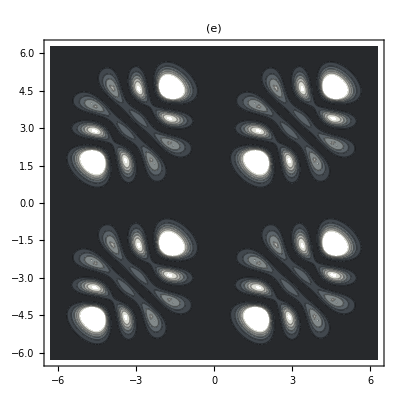

```mathematica
ContourPlot[Abs[WavefunctionFEM[y1,y2]]^2,{y1,-LSIZE*Pi,LSIZE*Pi},{y2,-LSIZE*Pi,LSIZE*Pi},ContourShading->Automatic,PlotPoints->45,ColorFunction-> "GrayTones",PlotLabel->"(e)",TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]
```

```mathematica
DensityFunctional=Plot[NIntegrate[Abs[WavefunctionFEM[y1,y2]]^2,{y2,-LSIZE*Pi,LSIZE*Pi}],{y1,-LSIZE*Pi,LSIZE*Pi},Frame->True]
```

$Aborted

(4.75 | 0. | 0.5 | 0. | 0. | 0.5
0. | 1.5 | 0. | 2.82843 | 0. | 0.
0.5 | 0. | 0.5 | 0. | 5.65685 | 0.5
0. | 2.82843 | 0. | 2.5 | 0. | 0.
0. | 0. | 5.65685 | 0. | 1.5 | 5.65685
0.5 | 0. | 0.5 | 0. | 5.65685 | 4.75)

```mathematica
TonksOrderParam[x_]:=Abs[WavefunctionFEM[x,x]]^2
TonksParameter=NIntegrate[TonksOrderParam[x],{x,-LSIZE*Pi,LSIZE*Pi}]
```

0.149865

```mathematica
(*Transition ie cos(x) matrix elements*)

Dp=Table[cmat[i,j],{i,1,STATENO},{j,1,STATENO}];
DipoleMatrix=Table[0.0,{i,1,15},{j,1,15}];

For[n=1,n≤15,n++,For[m=1,m≤n,m++,
Dm=Sum[Sum[(1/(√((1+Kdel[statetower[[k,1]],statetower[[k,2]]])*(1+Kdel[statetower[[l,1]],statetower[[l,2]]]))))*Evecs[[n]][[k]]*Evecs[[m]][[l]]*(Dp[[statetower[[k,1]],statetower[[l,1]]]]*Kdel[statetower[[k,2]],statetower[[l,2]]]+Dp[[statetower[[k,1]],statetower[[l,2]]]]*Kdel[statetower[[k,2]],statetower[[l,1]]]+Dp[[statetower[[k,2]],statetower[[l,2]]]]*Kdel[statetower[[k,1]],statetower[[l,1]]]+Dp[[statetower[[k,2]],statetower[[l,1]]]]*Kdel[statetower[[k,1]],statetower[[l,2]]]),{k,1,STATENO}],{l,1,STATENO}];
DipoleMatrix[[n,m]]=N[Dm,4];
DipoleMatrix[[m,n]]=N[Dm,4];

           ]];

MatrixForm[DipoleMatrix]
```

(-1.24853 | -0.28801 | 0.327599 | 0.0274036 | -0.273875 | -0.0168921 | -0.0499538 | -0.111154 | 0.0956359 | 0.124639 | 0.057701 | -0.0438091 | 0.0164832 | 0.0294469 | -0.00916638
-0.28801 | -1.31307 | -0.208866 | 0.378006 | 0.275367 | -0.226808 | -0.171253 | -0.161147 | -0.0376636 | 0.053684 | -0.0277685 | -0.0845426 | 3.1239×10^-16 | -0.0145047 | -0.014546
0.327599 | -0.208866 | -1.02886 | 0.0327458 | -0.14675 | 0.263639 | 0.407929 | 0.0373993 | 0.28809 | 0.0626929 | -0.0819063 | -0.0272492 | 0.196527 | -0.0208227 | -0.0270009
0.0274036 | 0.378006 | 0.0327458 | -1.13145 | 0.017729 | -0.197398 | 0.0486345 | -0.346572 | 0.0198377 | 0.000826083 | 0.236349 | 0.0196349 | 0.0710173 | 0.101378 | -0.10679
-0.273875 | 0.275367 | -0.14675 | 0.017729 | -0.810111 | 3.02657×10^-15 | -0.126511 | -0.227615 | 0.0682444 | -0.438711 | 3.02853×10^-15 | -0.0462694 | -0.226808 | 3.16989×10^-16 | -0.0198071
-0.0168921 | -0.226808 | 0.263639 | -0.197398 | 3.02657×10^-15 | -1.00664 | -0.0315012 | 0.128221 | 0.298229 | -3.06222×10^-16 | -0.269942 | 0.0485892 | 0.275367 | 0.185976 | -0.181557
-0.0499538 | -0.171253 | 0.407929 | 0.0486345 | -0.126511 | -0.0315012 | -0.645942 | 0.00605531 | -0.139401 | 0.0560019 | -0.252737 | 0.401569 | -0.0367411 | -0.0146557 | -0.233457
-0.111154 | -0.161147 | 0.0373993 | -0.346572 | -0.227615 | 0.128221 | 0.00605531 | -0.897076 | -0.0184167 | -0.0282734 | -0.129942 | -0.00746073 | 0.181263 | -0.0536612 | 0.00466217
0.0956359 | -0.0376636 | 0.28809 | 0.0198377 | 0.0682444 | 0.298229 | -0.139401 | -0.0184167 | -0.678695 | -0.0129626 | 0.0100576 | -0.0901904 | 0.165218 | 0.0260389 | -0.317088
0.124639 | 0.053684 | 0.0626929 | 0.000826083 | -0.438711 | -3.06222×10^-16 | 0.0560019 | -0.0282734 | -0.0129626 | -0.515931 | 6.10377×10^-16 | 0.0250631 | -1.85492×10^-16 | 2.96777×10^-15 | 0.00330446
0.057701 | -0.0277685 | -0.0819063 | 0.236349 | 3.02853×10^-15 | -0.269942 | -0.252737 | -0.129942 | 0.0100576 | 6.10377×10^-16 | -0.444038 | -0.00862666 | -4.90638×10^-16 | 0.40277 | 0.172008
-0.0438091 | -0.0845426 | -0.0272492 | 0.0196349 | -0.0462694 | 0.0485892 | 0.401569 | -0.00746073 | -0.0901904 | 0.0250631 | -0.00862666 | -0.294774 | 0.0214819 | -0.259845 | -0.0726073
0.0164832 | 3.1239×10^-16 | 0.196527 | 0.0710173 | -0.226808 | 0.275367 | -0.0367411 | 0.181263 | 0.165218 | -1.85492×10^-16 | -4.90638×10^-16 | 0.0214819 | -0.503677 | -5.25992×10^-16 | -0.142382
0.0294469 | -0.0145047 | -0.0208227 | 0.101378 | 3.16989×10^-16 | 0.185976 | -0.0146557 | -0.0536612 | 0.0260389 | 2.96777×10^-15 | 0.40277 | -0.259845 | -5.25992×10^-16 | -0.237342 | -0.0188401
-0.00916638 | -0.014546 | -0.0270009 | -0.10679 | -0.0198071 | -0.181557 | -0.233457 | 0.00466217 | -0.317088 | 0.00330446 | 0.172008 | -0.0726073 | -0.142382 | -0.0188401 | -0.182219)

0.159155

0.

```mathematica
DipoleMatrix[[1,3]]
DipoleMatrix[[3,7]]
```

0.327599

0.407929

```mathematica
DipoleMatrix[[1,5]]
DipoleMatrix[[5,13]]
```

-0.273875

-0.226808

1

```mathematica
(*0-1-2 ladder*)
E1=Evals[[1]];
E2=Evals[[2]];
E3=Evals[[3]];
E4=Evals[[4]];
E5=Evals[[5]];
E7=Evals[[7]];
E13=Evals[[13]];
E15=Evals[[15]];
wf=E15-E4;
ws=E4-E1;
Ratio=wf/ws
```

1.17873

3.6221

```mathematica
7.9                                  1.9226364021065196
8.0                                  1.9256324373039062
8.1                                  1.9286415929126977
8.5                                  1.9407671253231227
9.5                                   1.9711759611176964
10.4                                 1.9980748963520123
10.45                              1.9995486630315604
10.465                            1.9999903273965716
10.4653                          1.9999991584820558
10.465325                      1.99999989440195
10.4653275                   1.9999999679939013
10.465328                     1.9999999827122925
10.465329                     1.9999999827122925
10.465329001             2.0000000122962684
10.46532901                2.000000012443434
10.46532905                2.000000013620912
10.4653291                   2.0000000150927493
10.4653294                   2.0000000239237816
10.4653295                  2.000000026867469
10.46533                        2.000000041585855
10.46534                        2.000000335953587
10.46535                        2.000000630321234
10.4659                           2.000016820393738
10.466                             2.0000197640120634
10.4674                         2.0000609736600268
10.4675                          2.000063917134267
10.47                               2.0001375008669577
10.48                              2.000431775688986
10.5                                2.0010200362074437
```

-5.70979

-0.507264

0.0129883

```mathematica
(*Check the one particle problem*)
```

```mathematica
kappa=8.0;
SPTRUNC=10;(*N*)
DIM=2*SPTRUNC+1;
Hpend=Table[Honeptcl[i,j],{i,1,DIM},{j,1,DIM}];
ESysPend=Eigensystem[Hpend];


SortedEnergiesPend=ESysPend[[1]];
SortedCoeffPend=ESysPend[[2]];

(*Sort eigenvecotrs in increasing order of eigenvalue*)
For[i=1,i≤DIM,i++,
     For[j=i,j≤DIM,j++,

       If[SortedEnergiesPend[[i]]>SortedEnergiesPend[[j]],
            temp=SortedEnergiesPend[[i]];
            SortedEnergiesPend[[i]]=SortedEnergiesPend[[j]];
          SortedEnergiesPend[[j]]=temp;
        temp2=SortedCoeffPend[[i]];
     SortedCoeffPend[[i]] =SortedCoeffPend[[j]];
SortedCoeffPend[[j]]=temp2;      
    
,Continue]

]
]
SortedEnergiesPend
DipoleMatrixPend=Table[Sum[Sum[SortedCoeffPend[[i]][[k]]*SortedCoeffPend[[j]][[l]]*cmat[k,l],{k,1,DIM}],{l,1,DIM}],{i,1,DIM},{j,1,DIM}];
MatrixForm[DipoleMatrixPend]
```

{-6.06467,-2.33353,1.09281,4.20467,6.50217,9.82875,10.1652,16.5179,16.5222,25.3261,25.3261,36.2247,36.2247,49.1645,49.1645,64.1258,64.1258,81.1159,81.1159,100.825,100.825}

(-0.874846 | 0. | -0.166574 | 0. | -0.0230624 | 0. | 0.00776153 | 0. | 0.00136104 | 0. | 0.000110058 | 0. | -5.48833×10^-6 | 0. | 1.85366×10^-7 | -4.50891×10^-9 | 0. | 0. | 8.65678×10^-11 | 0. | -1.34157×10^-11
0. | -0.623495 | 0. | -0.275442 | 0. | 0.0536984 | 0. | -0.00832522 | 0. | 0.00070862 | 0. | -0.0000365653 | 0. | 1.26297×10^-6 | 0. | 0. | -3.11945×10^-8 | 6.00076×10^-10 | 0. | -7.63068×10^-11 | 0.
-0.166574 | 0. | -0.364533 | 0. | -0.350703 | 0. | 0.151792 | 0. | 0.0325091 | 0. | 0.0029708 | 0. | -0.000159423 | 0. | 5.64144×10^-6 | -1.41572×10^-7 | 0. | 0. | 2.73506×10^-9 | 0. | -2.91223×10^-10
0. | -0.275442 | 0. | -0.121268 | 0. | 0.440028 | 0. | -0.0952899 | 0. | 0.00948153 | 0. | -0.000532061 | 0. | 0.0000193204 | 0. | 0. | -4.928×10^-7 | 9.57671×10^-9 | 0. | -8.71712×10^-10 | 0.
-0.0230624 | 0. | -0.350703 | 0. | 0.29308 | 0. | 0.499882 | 0. | 0.162523 | 0. | 0.0177551 | 0. | -0.00103774 | 0. | 0.000038521 | -9.95744×10^-7 | 0. | 0. | 1.94581×10^-8 | 0. | -1.58265×10^-9
0. | 0.0536984 | 0. | 0.440028 | 0. | 0.166845 | 0. | 0.487769 | 0. | -0.0650672 | 0. | 0.00410221 | 0. | -0.000158096 | 0. | 0. | 4.17635×10^-6 | -8.2419×10^-8 | 0. | 5.72831×10^-9 | 0.
0.00776153 | 0. | 0.151792 | 0. | 0.499882 | 0. | 0.3642 | 0. | -0.473688 | 0. | -0.0650988 | 0. | 0.00414182 | 0. | -0.0001603 | 4.24464×10^-6 | 0. | 0. | -8.38606×10^-8 | 0. | 5.73891×10^-9
0. | -0.00832522 | 0. | -0.0952899 | 0. | 0.487769 | 0. | 0.131217 | 0. | 0.495234 | 0. | -0.040905 | 0. | 0.00175246 | 0. | 0. | -0.0000489065 | 9.91361×10^-7 | 0. | -5.14687×10^-8 | 0.
0.00136104 | 0. | 0.0325091 | 0. | 0.162523 | 0. | -0.473688 | 0. | 0.13538 | 0. | -0.495029 | 0. | 0.0408993 | 0. | -0.00175237 | 0.000048906 | 0. | 0. | -9.91372×10^-7 | 0. | 5.14601×10^-8
0. | 0.00070862 | 0. | 0.00948153 | 0. | -0.0650672 | 0. | 0.495234 | 0. | 0.0822526 | 0. | 0.498072 | 0. | -0.0281421 | 0. | 0. | 0.000876546 | -0.0000187279 | 0. | 7.04037×10^-7 | 0.
0.000110058 | 0. | 0.0029708 | 0. | 0.0177551 | 0. | -0.0650988 | 0. | -0.495029 | 0. | 0.0822707 | 0. | 0.498071 | 0. | -0.0281421 | 0.000876546 | 0. | 0. | -0.0000187279 | 0. | 7.04036×10^-7
0. | -0.0000365653 | 0. | -0.000532061 | 0. | 0.00410221 | 0. | -0.040905 | 0. | 0.498072 | 0. | 0.0564074 | 0. | 0.499064 | 0. | 0. | -0.0205807 | 0.000490013 | 0. | -0.0000138537 | 0.
-5.48833×10^-6 | 0. | -0.000159423 | 0. | -0.00103774 | 0. | 0.00414182 | 0. | 0.0408993 | 0. | 0.498071 | 0. | 0.0564074 | 0. | 0.499064 | -0.0205807 | 0. | 0. | 0.000490013 | 0. | -0.0000138537
0. | 1.26297×10^-6 | 0. | 0.0000193204 | 0. | -0.000158096 | 0. | 0.00175246 | 0. | -0.0281421 | 0. | 0.499064 | 0. | 0.0412063 | 0. | 0. | 0.499481 | -0.0157336 | 0. | 0.000378963 | 0.
1.85366×10^-7 | 0. | 5.64144×10^-6 | 0. | 0.000038521 | 0. | -0.0001603 | 0. | -0.00175237 | 0. | -0.0281421 | 0. | 0.499064 | 0. | 0.0412063 | 0.499481 | 0. | 0. | -0.0157336 | 0. | 0.000378963
-4.50891×10^-9 | 0. | -1.41572×10^-7 | 0. | -9.95744×10^-7 | 0. | 4.24464×10^-6 | 0. | 0.000048906 | 0. | 0.000876546 | 0. | -0.0205807 | 0. | 0.499481 | 0.0315884 | 0. | 0. | 0.499208 | 0. | -0.0133118
0. | -3.11945×10^-8 | 0. | -4.928×10^-7 | 0. | 4.17635×10^-6 | 0. | -0.0000489065 | 0. | 0.000876546 | 0. | -0.0205807 | 0. | 0.499481 | 0. | 0. | 0.0315884 | 0.499208 | 0. | -0.0133118 | 0.
0. | 6.00076×10^-10 | 0. | 9.57671×10^-9 | 0. | -8.2419×10^-8 | 0. | 9.91361×10^-7 | 0. | -0.0000187279 | 0. | 0.000490013 | 0. | -0.0157336 | 0. | 0. | 0.499208 | 0.0329373 | 0. | 0.479821 | 0.
8.65678×10^-11 | 0. | 2.73506×10^-9 | 0. | 1.94581×10^-8 | 0. | -8.38606×10^-8 | 0. | -9.91372×10^-7 | 0. | -0.0000187279 | 0. | 0.000490013 | 0. | -0.0157336 | 0.499208 | 0. | 0. | 0.0329373 | 0. | 0.479821
0. | -7.63068×10^-11 | 0. | -8.71712×10^-10 | 0. | 5.72831×10^-9 | 0. | -5.14687×10^-8 | 0. | 7.04037×10^-7 | 0. | -0.0000138537 | 0. | 0.000378963 | 0. | 0. | -0.0133118 | 0.479821 | 0. | 0.202309 | 0.
-1.34157×10^-11 | 0. | -2.91223×10^-10 | 0. | -1.58265×10^-9 | 0. | 5.73891×10^-9 | 0. | 5.14601×10^-8 | 0. | 7.04036×10^-7 | 0. | -0.0000138537 | 0. | 0.000378963 | -0.0133118 | 0. | 0. | 0.479821 | 0. | 0.202309)

{0.,0.,0.,0.,0.,-0.514905,-0.0994883,0.725873,-0.42804,0.120255,-0.0201205}

3.1